# Empirical Analysis of P vs. NP: On the Equivalence of Turing Machines as Partial Functions

Michael Sun

Wolfram Summer Research Program 2025

A Turing machine is a theoretical model of computation classified as an automaton invented by Alan Turing that operates on an infinite tape of sequential memory. The significance of Turing machines, as described in the Church-Turing thesis, comes from their ability to compute any function and therefore have the same computational ability as all conventional computers. Empirical evidence suggests that there exists Turing machines that follow different rules but ultimately compute the same function, presumably for all inputs. Naturally, these machines will have different runtimes, which models multiple computers running different algorithms to reach the same goal. Similarly, motivation for studying complexity theory comes from analyzing and improving algorithms. A central unsolved problem in the field is if quickly verifying a solution to a problem implies the existence of an algorithm that quickly solves it—commonly known as the P vs. NP problem. Analyzing patterns in the range of runtimes for equivalent Turing machines provides potential for empirically hypothesizing at the relationship between P and NP.

## Introduction

Formally, a Turing machine is a tuple containing a set of states, a halt state, a set of symbols called its alphabet, and a lookup table of all possible state-symbol pairs. Turing machines keep a pointer to the cell it is currently reading, and the symbol on this cell combined with its current state defines a transition. For each transition, three operations occur: read the symbol on the current cell, write a (not necessarily distinct) symbol to the current cell, and move to an adjacent cell. Certain traits of a Turing machine are difficult to quickly represent with a computer, so the results in this essay will be close approximations of the real behavior of Turing machines. Specifically, we will bound a finite section of the tape and set a halting condition not dependent on its state for convenience.

### Terminology

In this essay, the variables  and  generally refer to the  states and  symbols of a Turing machine, and the ordered pair  refers to an -state -symbol Turing machine. Additionally, we define setting a Turing machine to a nonnegative integer  as filling our chosen interval  of the tape of length  for some  with the binary representation of  in big endian (natural left-to-right order). We ensure that  (i.e. the number of bits fits in ). Additionally, we define the value of a Turing machine as the number created by each cell on  as base- digits where the blank symbol translates to zero (which is automatic in the Wolfram Language).

### Formalism

Let  be the set of all -state -symbol Turing machines. Each machine in  represents a partial function ⇀ on a fixed interval  of length  on the tape where  is the set of symbols and  is the set of input symbols. For this project, we set . Equivalently, this function can also be represented as ℕ⇀ℕ with input specified by the base  number formed on  where each symbol is an integer between 0 and . Define two Turing machines in  to be equivalent if they compute the same partial function on , or both do not exist. The number of distinct machines is the cardinality of . For each equivalence class, we will analyze patterns of the worst-case running times of each machine in the class and over all classes in  for different  and .

For example, the following 2-state 2-symbol Turing machine takes in  where 1’s are colored orange. The output is read as . It turns out that this rule always adds 1 to the input for our constraints.

Evolution of the partial function  described by rule 451 for ,  input  for 5 steps:

```mathematica
RulePlot[TuringMachine[445],{{1,4},{IntegerDigits[5,2,4],0}},5,ImageSize->Small]//Rasterize
```

-Graphics-

### Theory

Only certain  pairs are capable of simulating any other Turing machine starting from a blank tape. For example, any Turing machine with one symbol trivially fails to be universal because it will not edit the tape. Pairs that can simulate all other machines are known as universal Turing machines. Additionally, weakly universal Turing machines are machines that are universal on an arbitrary initial tape. Notably, the smallest of these machines are fully analyzable within computational constraints, such as , , and Wolfram’s  machine.

The universality of Turing machines as a mathematical model of computation revealed limits of computing, notably cases of logical (un)decidability. A problem is undecidable if and only if it is provable that there exists no algorithm that will always return the correct answer to the problem. Turing’s major result was his proof of the undecidability of determining if a computer program halts, famously known as the halting problem.

#### The Halting Problem and Rice’s Theorem

The usefulness of the undecidability of the halting problem is not only limited to the statement itself, but because many problems can be shown to be undecidable by reducing them to the halting problem. More notably, it is undecidable to determine if two Turing machines are equivalent, which necessitates the mentioned constraints. Similarly, the task to quickly analyze the behavior of a Turing machine without simulating it is a generalization of the halting problem known as Rice’s theorem, which implies that this task is generally undecidable. However, it does not say anything about determining relationships between machines, which we will see in a later section could contain a predictable pattern.

## Implementation

Due to the undecidability of universal static analysis and the computational irreducibility of Turing machine evolution, the implementation will inevitably be brute-force in nature. However, there are certain ways to prune the search space by examining only the rules. There are also optimizations for Turing machine simulation, particularly with memoizing sections of the tape.

### Prune

Despite the undecidability of finding a universal way of reducing computation across Turing machines or even on one Turing machine, we can take inspiration from DFA (deterministic finite automaton) minimization. Specifically, one big optimization we can make is to declare that all Turing machines with rules that permute a dead state (unreachable from the initial state) to be equal: each of these permutations are unreachable anyway.

The diagram below shows two equivalent Turing machines, each with a different permutation of the rules from state 2, which is unreachable from state 1.

```mathematica
GraphicsRow[{
Graph[{1->1,1->1,2->1,2->1,3->1,3->1},VertexLabels->Automatic],
Graph[{1->1,1->1,2->1,2->1,3->2,3->2},VertexLabels->Automatic]
},
ImageSize->Medium
]//Rasterize
```

-Graphics-

Determining the reachable nodes reduces to graph traversal. It is not hard to see that all state graphs have  vertices and  edges, resulting in a runtime of . Building this graph is straightforward by simply inspecting the full form of the Turing machine rule.

There are two ways to describe a Turing machine rule in the Wolfram Language: full form as a list of transitions, or an index as an integer. We want to take advantage of the language’s indexing method to skip over redundant rules. Increasing the index permutes rules in the following order: direction (-1 to 1), then symbol (0 to ), then state (1 to ). Notice that if the reachable states are consecutive (which must include state 1), we can permute the rest of the states that are unreachable without changing what the TM does. For example, a 3-state TM can only reach states 1 and 2, we can permute the rules from state 3, which defines a contiguous interval of rule numbers that are equivalent (i.e. rules 83520 to 84096 for a (3,2) TM). Thus, for each of these intervals we see, we can skip ahead to the end of the interval when we detect a beginning to avoid checking redundant rules.

The length of an iteration depends on the number of reachable states. If there are  reachable states from 1 to , then there are  unreachable states. The number of ways we can permute these unreachable states is given by , since there are  symbols per state and  ways to permute each single component of a rule. Notice  is the number of s-state k-symbol Turing machines.

Returns :

```mathematica
perm=Function[{d,s,k},(2s k)^(k(s-d))]
```

Function[{d,s,k},(2 s k)^(k (s-d))]

There exists resource functions for converting between the two forms of a Turing machine rule, but as we will see later, these functions are too slow, so I have taken their source code and written a compiled version. We will also declare perm in our environment so it can be used in compiled functions.

Reset the compiler environment:

```mathematica
$CompilerEnvironment=CreateCompilerEnvironment[];
```

#### Compiled TuringMachineFromNumber and TuringMachineToNumber

Function functions to be compiled:

```mathematica
TuringMachineFromNumberCompiledFn=Function[{n,s,k},
With[{l=Partition[IntegerDigits[n,2 s k,s k],k]},
Module[{fa=CreateDataStructure["FixedArray",s k],it=1},
Do[Do[
fa["Part",it++]={i,k-j}->{1,1,2} Mod[Quotient[l[[i,j]],{2k,2,1}],{s,k,2}]+{1,0,-1},
{j,k}],{i,s}];
fa["Elements"]
]
]
];
```

```mathematica
TuringMachineToNumberCompiledFn=Function[{rules,s,k},
Module[{fa=CreateDataStructure["FixedArray",s k]},
Do[
fa["Part",i]=(2Last[rules[[i]]][[2]]+Max[Last[Last[rules[[i]]]],0]+2k(First[Last[rules[[i]]]]-1)),
{i,s k}
];
FromDigits[Cast[fa["Elements"],"PackedArray"::["MachineInteger",1]],2s k]
]
];
```

Add to compilation environment:

```mathematica
CompilerEnvironmentAppendTo[{
FunctionDeclaration[
cfTuringMachineFromNumberCompiled,
Typed[{"MachineInteger","MachineInteger","MachineInteger"}->"ListVector"::["Rule"::["PackedArray"::["MachineInteger",1],"PackedArray"::["MachineInteger",1]]]]
@TuringMachineFromNumberCompiledFn
],
FunctionDeclaration[
cfTuringMachineToNumberCompiled,
Typed[{"ListVector"::["Rule"::["PackedArray"::["MachineInteger",1],"PackedArray"::["MachineInteger",1]]],"MachineInteger","MachineInteger"}->"MachineInteger"]@TuringMachineToNumberCompiledFn
]
}];
```

```mathematica
{TuringMachineFromNumberCompiled,TuringMachineToNumberCompiled}=
FunctionCompile[{
Function[{
Typed[n,"MachineInteger"],
Typed[s,"MachineInteger"],
Typed[k,"MachineInteger"]
},cfTuringMachineFromNumberCompiled[n,s,k]
],
Function[{
Typed[rules,"ListVector"::["Rule"::["PackedArray"::["MachineInteger",1],"PackedArray"::["MachineInteger",1]]]],
Typed[s,"MachineInteger"],
Typed[k,"MachineInteger"]
},cfTuringMachineToNumberCompiled[rules,s,k]
]
}];
```

#### Compiled Graph Build and DFS

To check which states we can reach from state 1, we can build a simple directed graph of states as an adjacency list and run a depth first search from state 1.

Build an adjacency list with s nodes and a list of edges e:

```mathematica
adjinit=Function[{s,e},
Module[{lll=CreateDataStructure["FixedArray",s],i},
Do[lll["Part",i]=CreateDataStructure["LinkedList"],{i,s}];
Do[With[{u=First[e[[i]]],v=Last[e[[i]]]},If[u!=v,lll[[u]]["Append",v];0,0]],{i,Length[e]}];
#["Elements"]&/@lll["Elements"]
]
];
```

For example, the adjacency list for rule 64 for a 2-state 2-symbol TM (the graph depicted on the left in the section head) is given by the following, which shows that state 1 has no neighbors while state 2 can reach state 1 in two ways.

```mathematica
adjinit[2,TuringMachineFromNumberCompiled[64,2,2][[All,All,1]]]
```

{{},{1,1}}

DFS is simply a recursive function, defined below.

```mathematica
dfs=Function[{adj,u,s},
Module[{vis=ConstantArray[0,s],dfs,reached=CreateDataStructure["LinkedList"]},
dfs=Function[{v},If[vis[[v]]==0,vis[[v]]=1;reached["Append",v];If[Length[adj[[v]]]>0,dfs/@adj[[v]]]];0];
dfs[u];
reached["Elements"]
]
];
```

Running DFS on the above adjacency list from states 1 and 2 shows that state 1 can only reach itself while state 2 can reach both states.

```mathematica
dfs[,#,2]&/@{1,2}
```

{{1},{2,1}}

Add to compilation environment:

```mathematica
CompilerEnvironmentAppendTo[{
FunctionDeclaration[
cfadjinit,Typed[{"MachineInteger","ListVector"::["Rule"::["MachineInteger","MachineInteger"]]}->"ListVector"::["ListVector"::["MachineInteger"]]]
@adjinit
],
FunctionDeclaration[
cfdfs,
Typed[{"ListVector"::["ListVector"::["MachineInteger"]],"MachineInteger","MachineInteger"}->"ListVector"::["MachineInteger"]]
@dfs
]
}];
```

```mathematica
{adjinitCompiled,dfsCompiled}=FunctionCompile[{
Function[{
Typed[s,"MachineInteger"],
Typed[e,"ListVector"::["Rule"::["MachineInteger","MachineInteger"]]]
},cfadjinit[s,e]
],
Function[{
Typed[adj,"ListVector"::["ListVector"::["MachineInteger"]]],
Typed[u,"MachineInteger"],
Typed[s,"MachineInteger"]
},cfdfs[adj,u,s]
]
}];
```

#### Compiled Transform and Other Functions

The key construction will be to point all unreachable states to 1’s so that they map to the beginning of an equivalent block of rules if the condition is satisfied, so if we change the output state/symbol/direction tuple for an unreachable state, the output of transform will stay the same. This allows us to directly convert this rule to the rule number that represents the start of a potential block of rules with unreachable states.

Creates a key for a Turing machine such that equivalent have the same key:

```mathematica
transform=Function[{s,k,reach,rout},
Flatten[Table[If[
MemberQ[reach,j],
Table[rout[[kk]],{kk,k(j-1)+1,k*j}],
Table[{1,0,-1},k]
],{j,s}],1]
];
```

For example, we know that the Turing machines from 0 to 63 are equivalent and from 64 to 127 are equivalent, which is consistent with the output of transition.

```mathematica
Equal@@@TakeDrop[Table[transform[2,2,{1},TuringMachineFromNumberCompiled[i,2,2][[All,2]]],{i,0,127}],64]
```

{True,True}

Finally, to determine how far to jump, we need a function to check if a list is consecutive to apply it to the list of reachable states as described in the beginning of this section, which is defined below.

Checks if l is consecutive:

```mathematica
consQ=Function[l,Most[l]+1===Rest[l]];
```

```mathematica
CompilerEnvironmentAppendTo[{
FunctionDeclaration[
cfperm,
Typed[{"MachineInteger","MachineInteger","MachineInteger"}->"MachineInteger"]
@perm
],
FunctionDeclaration[
cftransform,Typed[{"MachineInteger","MachineInteger","PackedArray"::["MachineInteger",1],"PackedArray"::["MachineInteger",2]}->"PackedArray"::["MachineInteger",2]]
@transform
],
FunctionDeclaration[
cfconsQ,
Typed[{"PackedArray"::["MachineInteger",1]}->"Boolean"]
@consQ
]
}];
```

#### Compiled Pruning Function

The following function is a block of procedural code that determines the number of unique rules and the number of times each rule is repeated. To dynamically skip blocks of rules, we   must use a For loop to have control over the index. To determine if the current rule is the start of a block, we do a graph traversal in  time, which is done  times.

Takes in the number of rules to analyze from 0 to len-1 and loops through those rules, skipping if possible:

```mathematica
cfprune=FunctionCompile[Function[{
Typed[len,"MachineInteger"],
Typed[s,"MachineInteger"],
Typed[k,"MachineInteger"]
},
Module[{i,map=CreateDataStructure["HashTable"]},
For[i=0,i<len,i++,
With[{rule=cfTuringMachineFromNumberCompiled[i,s,k]},
With[{vout=Cast[
cfdfs[cfadjinit[s,
Module[{a=CreateDataStructure["FixedArray",s k]},
Do[a["Part",i]=First[rule[[i]]][[1]]->Last[rule[[i]]][[1]],{i,s k}];
a["Elements"]
](* returns rule[[All,All,1]] *)
],1,s],
"PackedArray"::["MachineInteger",1]]
},
map["Insert",(#->If[cfconsQ[Sort[vout]],
(i+=#-1;#)&@cfperm[Length[vout],s,k],1]
+If[map["KeyExistsQ",#],map["Lookup",#],0])&
@cfTuringMachineToNumberCompiled[
With[{
left=Transpose[{
Flatten[Table[ConstantArray[j,k],{j,s}]],
Table[Mod[j,k],{j,s k-1,0,-1}]
}],
right=cftransform[s,k,vout,Cast[Last/@rule,"PackedArray"::["MachineInteger",2]]]
},
Module[{a=CreateDataStructure["FixedArray",s k]},
Do[a["Part",i]=left[[i]]->right[[i]],{i,s k}];
a["Elements"]
]
],s,k
]
];
]
]
];
map["Elements"]
]
]];
```

```mathematica
elems=cfprune[perm[0,2,2],2,2];
```

```mathematica
elems23=cfprune[perm[0,2,3],2,3];
```

Gets elems for (s,k)=(3, 2) from the cloud:

```mathematica
elems=CloudGet[CloudObject[["https://www.wolframcloud.com/obj/18a0dc05-36a4-42da-b07c-fd940256d0f4"](https://www.wolframcloud.com/obj/18a0dc05-36a4-42da-b07c-fd940256d0f4)]];
```

We can confirm that consecutive equivalence classes come in sizes of  for all . In this case, for , we indeed have , , .

```mathematica
DeleteDuplicates[elems23[[All,2]]]
```

{1,144,20736}

### Search

As mentioned, the behavior of a Turing machine is undecidable even on a finite tape, so we must optimize our simulation method. One notable bottleneck—amongst others—is repeating and non-terminating Turing machines. Optimizing repeating machines can be “solved” by memoizing a “snapshot” of the Turing machine for each independent round of simulation of a machine and an input, and after each iteration, we check if the current snapshot has been seen before. However, this “solution” does not address the main bottleneck of the program, which is that it has to construct the TM tape for each step in its iteration, which is an  operation. Therefore, I have written a compiled version of the TuringMachine function that only returns the part of the tape we want after the TM halts.

Compiled TM function that returns a pair of {{a1,a2,...},{runtime}}:

```mathematica
TuringMachineCompiledSimple=
With[{arrtype="PackedArray"::["MachineInteger",1]},
FunctionCompile[
Function[{
Typed[rule,"ListVector"::["Rule"::[arrtype,arrtype]]],
Typed[tminit,arrtype],
Typed[tapeinit,arrtype],
Typed[default,"MachineInteger"],
Typed[t,"MachineInteger"]
},
With[{tlen=Length[tapeinit],s=tminit[[1]],x=tminit[[2]]},
Module[{
rulemap=CreateDataStructure["HashTable"::[arrtype,arrtype]],
state=s,head=x,
writ=CreateDataStructure["HashTable"::["MachineInteger","MachineInteger"]],
next,hmin=1,
i
},
Do[rulemap["Insert",rule[[i]]],{i,Length[rule]}];
Do[If[tapeinit[[i]]!=default,writ["Insert",i->tapeinit[[i]]]],{i,tlen}];
For[i=2,i<=t+1&&head<=x,i++,
next=rulemap["Lookup",{state,If[writ["KeyExistsQ",head],writ["Lookup",head],default]}];
state=First[next];
writ["Insert",head->next[[2]]];
head+=Last[next];
hmin=Min[hmin,head];
];
With[{lpad=1-hmin,tape=CreateDataStructure["FixedArray"::["MachineInteger"],tlen+1-hmin]},
Do[tape["Part",i]=If[writ["KeyExistsQ",i-lpad],writ["Lookup",i-lpad],default],{i,tlen+lpad}];
{Cast[tape["Elements"],arrtype],{If[i==t+2,-1,i-2]}}
]
]
]
]
]
];
```

Get the halting times and halting values for all bits bit numbers. Returns a pair of the halting times and halting values in that order:

```mathematica
getHalts[{rule_Integer,s_Integer,k_Integer},bits_Integer,steps_Integer]:=
Transpose[Table[
(If[First[#2]==-1,{-1,-1},{First[#2],FromDigits[#1,k]}])&
@@TuringMachineCompiledSimple[
TuringMachineFromNumberCompiled[rule,s,k],
{1,Max[1,IntegerLength[i,k]],0},
IntegerDigits[i,k],
0,
steps
],
{i,0,2^bits-1}
]]
```

Call function in parallel. Wolfram internal parallelization functions should preserve order:

```mathematica
halts=ParallelMap[getHalts[{#,2,2},8,1000]&,elems[[All,1]]];
```

```mathematica
halts23=ParallelMap[getHalts[{#,2,3},6,200]&,elems23[[All,1]]];
```

Join the computed information where each element in the list is in the form{rule, number times repeated, {halt times}, {halt values}}:

```mathematica
haltconfig=Transpose[{
elems[[All,1]],
elems[[All,2]],
halts[[All,1]],
halts[[All,2]]
}];
```

```mathematica
haltconfig23=Transpose[{
elems23[[All,1]],
elems23[[All,2]],
halts23[[All,1]],
halts23[[All,2]]
}];
```

Get the MX file created by DumpSave compressed with XZ 5.4.5 liblzma 5.4.5 of the halting configuration of (2,3) TMs:

```mathematica
xzfile=CloudGet[CloudObject[["https://www.wolframcloud.com/obj/michaelsunsd/haltconfig23.mx.xz"](https://www.wolframcloud.com/obj/michaelsunsd/haltconfig23.mx.xz)]];
```

Load the file:

```mathematica
<<path/to/decompressed/xzfile.mx
```

Association from rule to {{halt times},{halt values}}:

```mathematica
halts=Association[First[#]->#[[3;;4]]&/@haltconfig];
```

```mathematica
halts23=Association[First[#]->#[[3;;4]]&/@haltconfig23];
```

Gather the halting configurations by equivalency using their outputs of the form {{range, min, max, size, rules...}...}:

```mathematica
haltgroups22=Map[
With[{mm=MinMax[Max[#[[3]]]&/@#]},
Flatten[{mm[[2]]-mm[[1]],mm,Total[#[[All,2]]],#[[All,1]]}]
]&,
GatherBy[
Select[haltconfig,Max[#[[3]]]>=0&],
#[[4]]&
]
];
```

```mathematica
haltgroups23=Map[
With[{mm=MinMax[Max[#[[3]]]&/@#]},
Flatten[{mm[[2]]-mm[[1]],mm,Total[#[[All,2]]],#[[All,1]]}]
]&,
GatherBy[
Select[haltconfig23,Max[#[[3]]]>=0&],
#[[4]]&
]
];
```

In this scheme, there are 748 (2,2) TM’s that do not halt, and there 353 different functions that can be computed. Stephen Wolfram in NKS found there to be 351 different TM’s, which may be caused by a slight difference in constraints and setup.

```mathematica
perm[0,2,2]-Total[haltgroups22[[All,4]]]
```

748

```mathematica
Length[haltgroups22]+1
```

353

For (2,3) TM’s, there are this many machines that don’t halt,

```mathematica
perm[0,2,3]-Total[haltgroups23[[All,4]]]
```

225263

and this many different functions

```mathematica
Length[haltgroups23]+1
```

448401

## Runtime Distribution Analysis

In this section, we visualize our computed results and draw attention to global relationships between each computed function and their runtimes. Note that all data fetched from the cloud were computed using the code in the previous section.

##### Manipulable Plot (very slow and essentially unresponsive for (s,k)>(2,2))

Generates a manipulable plot of equivalence class size, runtime range, and runtime min/max:

```mathematica
genManip[data_List,maxlen_Integer:500]:=
With[{
rb=Min[Length[data],maxlen],
step=IntegerPart[Min[Length[data],maxlen]/400],
sizstep=Quotient[Max[Length/@data],400]
},
Manipulate[
With[{
w=1000,
sorted=Take[SortBy[data,
Switch[
sort,
"Runtime Range",-First[#]&,
"Class Size",-#[[4]]&,
"Max Runtime",-#[[3]]&,
"Min Runtime",-#[[2]]&
]
],UpTo[maxlen]]
},
Column[{
ListStepPlot[
sorted[[IntegerPart[Min[a,b]];;IntegerPart[b],4]],
Filling->Bottom,
PlotRange->All,
ImageSize->{w,Automatic},
AspectRatio->1/16,
PlotLabel->"Equivalence Class Size"
],
ListStepPlot[
(First/@sorted)[[IntegerPart@Min[a,b];;IntegerPart@b]],
Filling->Bottom,
PlotRange->All,
ImageSize->{w,Automatic},
AspectRatio->1/10,
PlotLabel->"Runtime Range"
],
ListStepPlot[{
sorted[[IntegerPart[Min[a,b]];;IntegerPart[b],2]],
sorted[[IntegerPart[Min[a,b]];;IntegerPart[b],3]]
},
Filling->{2->{1}},
PlotRange->All,
ImageSize->{w,Automatic},
AspectRatio->1/6,
PlotLabel->"Maximum and Minimum Runtime",
PlotLegends->{"Min","Max"}
]
}]
],
{{a,1,"Left bound"},1,rb,step,Appearance->"Labeled"},
{{b,rb,"Right bound"},1,rb,step,Appearance->"Labeled"},
{{sort,"Runtime Range","Sort by"},{"Runtime Range","Class Size","Max Runtime","Min Runtime"}},
SaveDefinitions->True
]
]
```

##### Static Plot

Generates a static plot of equivalence class size, runtime range, and runtime min/max for a given sort method:

```mathematica
genPlot[data_List,maxlen_Integer:∞,sort_String:"Runtime Range"]:=
With[{
w=1000,
sorted=Take[SortBy[data,
Switch[
sort,
"Runtime",-First[#]&,
"Size",-#[[4]]&,
"Max",-#[[3]]&,
"Min",-#[[2]]&
]
],UpTo[maxlen]]
},
Column[{
ListStepPlot[
sorted[[All,4]],
Filling->Bottom,
PlotRange->All,
ImageSize->{w,Automatic},
AspectRatio->1/16,
PlotLabel->"Equivalence Class Size"
],
ListStepPlot[
(First/@sorted),
Filling->Bottom,
PlotRange->All,
ImageSize->{w,Automatic},
AspectRatio->1/10,
PlotLabel->"Runtime Range"
],
ListStepPlot[{
sorted[[All,2]],
sorted[[All,3]]
},
Filling->{2->{1}},
PlotRange->All,
ImageSize->{w,Automatic},
AspectRatio->1/6,
PlotLabel->"Maximum and Minimum Runtime",
PlotLegends->{"Min","Max"}
]
}]
]
```

Plot the first 2000 groups of (2,3) TM data sorted by runtime range:

```mathematica
genPlot[haltgroups23,2000,"Runtime"]//Rasterize
```

-Graphics-

Plot the first 2000 groups of (2,3) TM’s sorted by maximum runtime:

```mathematica
genPlot[haltgroups23,2000,"Max"]//Rasterize
```

The plots of (3, 2) and (2, 3) Turing machines look almost identical so (2, 3) will be omitted in this essay but can be generated with the code below.

Get and plot (2,2) data:

```mathematica
genManip[haltgroups22]
```

(4,2) plot for the first 68 million rules (the first 67108864 being split into four groups):

```mathematica
haltgroups42=CloudGet[CloudObject[["https://www.wolframcloud.com/obj/70c01f90-a92b-4ca9-9cd4-e516dc85ba31"](https://www.wolframcloud.com/obj/70c01f90-a92b-4ca9-9cd4-e516dc85ba31)]];
genplot[haltgroups42]
```

(3,3) plot for the first 206 million Turing machines (the first 204073344 being split into six groups):

```mathematica
haltgroups33=CloudGet[CloudObject[["https://www.wolframcloud.com/obj/1e1e1e10-681c-4346-b486-2ec3b138be09"](https://www.wolframcloud.com/obj/1e1e1e10-681c-4346-b486-2ec3b138be09)]];
genplot[haltgroups33]
```

Notice that the shape of the minimum and maximum curves look almost identical in all  combinations presented here. Also, all plots have tall spikes on the right when sorting by runtime range where the runtime range is near zero. Sorting by class size, we see that each plot ends with an increasing curve, which represents the mentioned spikes in maximum runtime despite having very small class size. We also observe that given that the size of a set of equivalence classes is “sufficiently large”, the distribution of runtime ranges is seemingly unpredictable. See the (2,3) or (3,2) plots from 1 to 500 and (3,3) plot from 1 to 1000.

### Rule Distribution

The following graphic depicts the distribution of rule numbers for the first 256 equivalence groups sorted from greatest runtime range to least. Each point  means that rule  is part of equivalence class , with many y-values for each x-value. Points near each other with the same color correspond to the same equivalence class.

```mathematica
stackPoints[l_List]:=MapIndexed[Function[{value,index},{First@index,#}&/@value]]@l
```

```mathematica
Rasterize[
ListPlot[
stackPoints[SortBy[haltgroups23,-First[#]&][[;;256,4;;]]],
PlotRange->Full,
ImageSize->{1200,Automatic},
AspectRatio->1/3,
PlotLabel->"Distribution of the First 256 Equivalence Classes, Sorted by Runtime Range",
PlotHighlighting->None,
AxesLabel->{"Equivalence class", "Rule number"},
PerformanceGoal->"Speed"
]
]
```

-Graphics-

We notice that many equivalence classes contain consecutive blocks of rules—which do not contain the blocks we pruned out. Additionally, there are areas with small between pseudo-consecutive rules belonging to the same equivalence class, such as the green lines near the beginning. Non-consecutive sets of rules that have unreachable states in their state graph form an arithmetic sequence and would have regularity on the graphic, but the intriguing part is that cases of unreachable states are relatively uncommon, yet for almost all equivalence classes shown, there is some form of regularity.

## Runtime Analysis

Each equivalence class corresponding to a single -coordinate on the graphs above contain rules that differ in runtime despite computing the same function. This can be visualized by plotting a TM’s runtime against the value of the input on the tape, and we can overlay graphs of common runtimes with manipulable parameters to manually match a runtime plot with a function. In our scheme, if the function an equivalence class produces is undefined on an input , the  coordinate drops to -1.

##### Functions to generate the plots below

Generate a plot for the runtime of each rule in an equivalence class, optionally with an overlay of a function:

```mathematica
runtimePlot[rules_List,eqn_List,var_,mode_String:"None"]:=
With[{data=DeleteDuplicates[(If[mode=="None",#,compress[#,Switch[mode,"Mean",Mean,_,Max]]]&@First[halts[#]])&/@rules]},
Show[
Apply[Sequence,Plot[
#,{var,0,Length[First[data]]-1},
PlotRange->All,
PlotStyle->{Dashed,Thickness[0.0025]},
PlotLabels->"Expressions"
]&/@eqn
],
ListStepPlot[
data,
DataRange->{0,Length[First[data]]-1},
Filling->Bottom,
PlotRange->All
],
AspectRatio->1/2,
ImageSize->Large,
ImagePadding->{{30,100},{20,50}},
AxesLabel->{"Input number", "Runtime"}
]
]
runtimePlot[rules_List,mode_String:"None"]:=runtimePlot[rules,{},x]
```

Generate a manipulable plot for each rule in an equivalence class:

```mathematica
runtimeManip[rules_List,mode_String:""]:=
With[{data=DeleteDuplicates[(If[mode=="",#,compress[#,Switch[mode,"Mean",Mean,_,Max]]]&@First[halts[#]])&/@rules]},
With[{len=Length[First[data]]},
Manipulate[
Show[
Plot[dy,{x,0,len},PlotStyle->{Dashed,Thickness[0.0025]}],
Plot[loga*Log2[x+1]+dy,{x,0,len},PlotStyle->{Dashed,Thickness[0.0025]}],
Plot[lina*x+dy,{x,0,len},PlotStyle->{Dashed,Thickness[0.0025]}],
Plot[qa*x^qp+dy,{x,0,len},PlotStyle->{Dashed,Thickness[0.0025]}],
Plot[ea*2^x+dy,{x,0,len},PlotStyle->{Dashed,Thickness[0.0025]}],
ListStepPlot[
data,
DataRange->{0,Length[First[data]]},
Filling->Bottom,
PlotRange->All
],
PlotRange->{{0,len},{0,Max[data]}},
AspectRatio->1/2,
ImageSize->Large,
ImagePadding->All,
AxesLabel->{"Input number", "Runtime"}
],
{{dy,0,"y shift"},0,Max[data],Appearance->"Labeled"},
{{loga,1,"Logarithmic coefficient"},1,30,Appearance->"Labeled"},
{{lina,1,"Linear coefficient"},0.1,10,Appearance->"Labeled"},
{{qa,1,"Polynomial coefficient"},0.1,10,Appearance->"Labeled"},
{{qp,1,"Polynomial exponent"},0.1,10,Appearance->"Labeled"},
{{ea,1,"Exponential coefficient"},0.1,10,Appearance->"Labeled"},
SaveDefinitions->True
]
]
]
```

### Note

There may be a fundamental issue with this approach of modeling runtime, however, since there is no obvious reason why Turing machines should have longer runtimes if the number on its tape is increased---everything is governed as a set of transitions that has no obvious regard to the “size” of the number on the tape. Only for a few TM’s that simulate simple processes (e.g. incrementing a number) will they have the emergent behavior of runtime dependent on the size of its input. But as we will see, most TM’s will not have this behavior but rather have asymptotically constant runtime. Therefore, we will first analyze runtime based on the value of the tape, then revert to the more orthodox way of interpreting TM runtime by using the length of the input (which is the scheme in NKS), since we generally view the tape as an array of symbols rather than a single value.

However, both approaches will inevitably result in some cyclic behavior at some point but is unlikely to be reached given our constraints, as we have only simulated 6 bit numbers. Suppose a certain TM  operates within positions 0 to 10 on its tape within  steps on a tape full of zeros. Then if we set the symbols on cells farther than cell 10 it would make no difference to the machine within  steps, which means .

We begin by analyzing runtime by plotting against the value of the initial tape.

### (2,2) TM’s

Get sorted equivalence classes by runtime range:

```mathematica
sorted22=ReverseSortBy[haltgroups22,First];
```

Plotting the runtime of all rules for a function may obscure features of some plots, so we alternatively visualize a function by plotting each rule separately with the function below.

Generates a list of runtime plots from a list of rule numbers:

```mathematica
plotSeparate[rules_List,mode_String:"None",halts_Association:halts]:=
Map[
First[#]->Rasterize[
ListStepPlot[Last[#],Filling->Bottom,PlotRange->All,Axes->{False,True}],
ImageSize->Small
]&,
ReverseSortBy[DeleteDuplicatesBy[(#->(If[mode=="None",#,compress[#,Switch[mode,"Mean",Mean,_,Max]]]&@First[halts[#]]))&/@rules,Last],Max[Last[#]]&]
]
```

The following graphics depict the runtime plot of a TM with a certain rule number for each group sorted by runtime range. In each plot, the runtime for the TM is plotted against the value of the input on the tape. The plots are ordered from largest max runtime to smallest max runtime.

Runtime plots for the first group sorted by runtime range (the group with the largest runtime range):

```mathematica
plotSeparate[sorted22[[1,5;;]]][[{1,3,7,8}]]
```

{2289→-Graphics-,2273→-Graphics-,1949→-Graphics-,4074→-Graphics-}

This is a neat example. Notice how the runtime for rules 1953 and 2289 increases asymptotically linearly but at some spots have much shorter runtimes. Rules 1969 and 2273 increase approximately logarithmically also with gaps, and the rest of the functions run in small constant time. Just as a sanity check, these plots agree with what we see if we simulate each of these rules on a TM with the number 7 in binary on the tape.

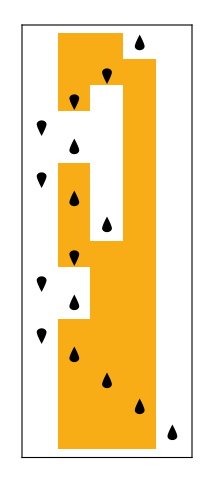
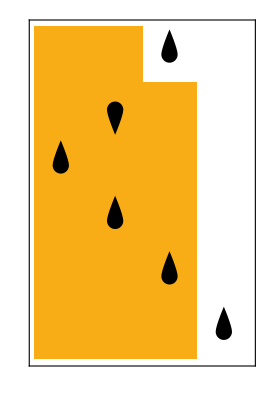
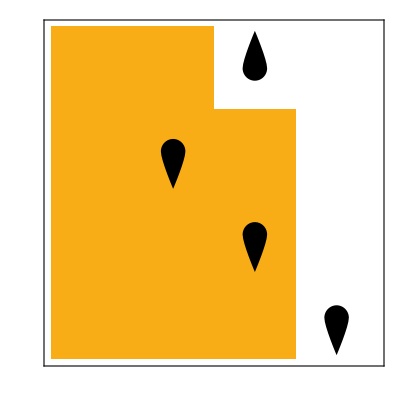
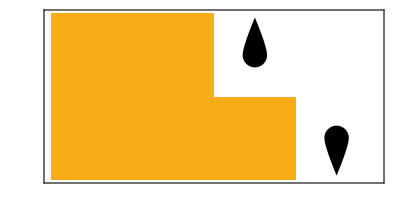

```mathematica
RulePlot[TuringMachine[#1],{{1,IntegerLength[6,2]},{IntegerDigits[6,2],0}},#2]&@@@{{1953,15},{1939,5},{3517,3},{4074,1}}
```

Merged runtime plot showing the worse case linear growth rate:

```mathematica
runtimePlot[sorted22[[1,5;;]],{2x},x]
```

-Graphics-

Another group worth pointing out is the 15th function shown below, where there are TM’s that grow logarithmically and also constant, which is another example of where a non-constant algorithm can be improved to constant. However, most of the first 40 functions are simply computed by TM’s with the same asymptotic runtime but at different magnitudes, which I hypothesize means that for non-trivial functions, most improvements are going to be reductions by a constant factor instead of in growth rate.

Separate runtime plots for select TM’s in the 15th function:

```mathematica
plotSeparate[sorted22[[15,5;;]]][[{1,5,6}]]
```

{1341→-Graphics-,3389→-Graphics-,3919→-Graphics-}

We can also sort by maximum runtime:

```mathematica
sorted22max=SortBy[haltgroups22,-#[[3]]&];
```

Generates plots for the first 36 groups sorted by maximum runtime:

```mathematica
Table[i->plotSeparate[sorted22max[[i,5;;]]],{i,36}]//Column
```

If we generate the separated plots for the first 36 functions (with the function above), observe that most of these functions are only computed by a single or a few TM’s, which may represent problems that are intrinsically difficult to even find a solution for. However, the 29th and 36th functions are interesting in that both are computed by 9 different TM’s, and all of those run in logarithmic time, which represents a more non-trivial function where there are many known solutions but none of them are trivially fast. Strangely, both of these functions trace the same graph...

Runtime plot for the 29th and 36th function, respectively:

```mathematica
Rasterize[runtimePlot[sorted22max[[#,5;;]],{5.8Log2[x+1]},x],ImageSize->Medium]&/@{29,36}
```

{-Graphics-,-Graphics-}

Now we can observe that the peaks of the maximum runtime of function 1 sorted by range and 29 and 36 (and presumably 15) sorted by max occur when the input are around powers of 2 (for function 1, it’s one less than a power of 2). Notice that the numbers represented with a minimum of  bits are between  and , so this brings us to the second way of viewing “input size”: using the length of the input. For each group of inputs represented by some  bits, we take the maximum (or average) of the runtime to get the max/average runtime by input length. This method of evaluating runtime is much cleaner, since the jagged linear function will become a clean exponential, and similarly logarithm to linear.

Compress a list of running times by combining the runtimes of inputs of a certain length with function fn. This defines the compression function in plotSeparate and runtimePlot:

```mathematica
compress[data_List,fn_:Max]:=(fn/@TakeList[data,Table[2^k,{k,0,Log2[Length[data]+1]-1}]])
```

Plotting by length, we indeed see that the linear function becomes exponential and the logarithm becomes linear. Similarly, taking the average of runtimes for a given length will result in an approximately linear and logarithmic graph like the uncompressed visualization.

```mathematica
Append[plotSeparate[sorted22[[1,5;;]],"Max"][[{1,3,6,7}]],Rasterize[runtimePlot[sorted22[[1,5;;]],{2^(x+2)},x,"Max"],ImageSize->Medium]]
```

{1953→-Graphics-,1969→-Graphics-,1949→-Graphics-,4074→-Graphics-,-Graphics-}

### (2,3) TM’s

```mathematica
sorted23=ReverseSortBy[haltgroups23,First];
```

```mathematica
Length[sorted23[[1]]]
```

76

```mathematica
plotSeparate[sorted23[[1,5;;]],halts23]
```

{1132264→-Graphics-,635810→-Graphics-,219590→-Graphics-,179572→-Graphics-,1173371→-Graphics-,717419→-Graphics-,1215209→-Graphics-,1215208→-Graphics-,677283→-Graphics-,677282→-Graphics-,1214855→-Graphics-,1132262→-Graphics-,677285→-Graphics-,138232→-Graphics-,138148→-Graphics-,138100→-Graphics-,136646→-Graphics-,1214927→-Graphics-,1214843→-Graphics-,717131→-Graphics-,677291→-Graphics-,676091→-Graphics-,675947→-Graphics-,675803→-Graphics-,1133474→-Graphics-,634600→-Graphics-,1174900→-Graphics-,717254→-Graphics-,219755→-Graphics-,178043→-Graphics-,1174946→-Graphics-,717544→-Graphics-,1133428→-Graphics-,634310→-Graphics-,219515→-Graphics-,178283→-Graphics-,1174947→-Graphics-,1174949→-Graphics-,1133476→-Graphics-,717542→-Graphics-,635894→-Graphics-,178427→-Graphics-,717551→-Graphics-,219467→-Graphics-,179579→-Graphics-,178139→-Graphics-}

#### boyer moore thing we dont need anymore

Additionally, if we sort by average runtime instead of maximum runtime and plot the top 10 groups again, notice how most of these functions are again simply large constants. That is, except the first one, which exhibits interesting behavior.

Notice that for this function, we see three types of plots: decreasing, constant, and increasing plots where there is an approximately equal number of decreasing and increasing plots. When will an algorithm ever have a decreasing runtime? We bring up two potential cases, one of which can be a puzzle solver. For example, a sudoku puzzle with more clues generally will generally be easier and thus generally decrease with input size (but also may be harder sometimes depending on how the puzzle is designed. We also disregard that a sudoku puzzle must have at least 17 clues...). The better and more well-known example is the Boyer-Moore string search algorithm, which runs faster when the search pattern is longer. Disregarding the constant runtimes for now, this function provides a good example of when different algorithms do better in different scenarios. For very short patterns, we can use algorithms the behave like rule 2201 (e.g. linear search, KMP), but for longer patterns, we can leverage algorithms like rule 433 (if we have knowledge of them). 

Of course, this is the very rare case and, as mentioned before, most of the other functions are simply large constants, which prompts us to modify our sorting method to extract functions that are increasing.

#### old

```mathematica
runtimePlot[sorted22[[13]],2,2,8]
```

runtimePlot[{34,3,37,4,2549,2261,2293,2517},2,2,8]

Out of the first 20 equivalence classes for (2,2) machines, 10 groups generally had logarithmic behavior, and some groups seem to oscillate from 0 to a constant maximum. It is difficult to extrapolate the ultimate behavior of these oscillating plots, but I suspect they are most likely constant and possibly logarithmic. One of these graphs is group 2 (see below), which seems to model a triangle wave and thus be considered constant. However, group 10 may imply that the graphs like group 2 (potentially excluding itself) may be part of a larger graph that only becomes emergent for large inputs.

```mathematica
Block[{states=2,symbols=2,width=32},
With[
{
dx=2.5,
bits=8,
data=DeleteDuplicates[
ParallelMap[
htDP[#,10,8,64]&,
sorted22[[2,4;;]]
][[All,1]]
]
},
ListPlot[
data,
DataRange->{0,Length@data[[1]]-1},
Joined->True,
PlotRange->All,
AspectRatio->1/6,
ImageSize->{1000,Automatic},
AxesOrigin->{0,0},
AxesLabel->{"Input number", "Runtime"},
PlotLabel->"(2,2) group 2 runtime",
PerformanceGoal->"Speed"
]
]
]//Rasterize
```

-Graphics-

```mathematica
Block[{states=2,symbols=2},
With[
{
dx=2.5,
bits=8,
data=DeleteDuplicates[
ParallelMap[
htDP[#,8,8,64]&,
sorted22[[10,4;;]]
][[All,1]]
]
},
Show[
Plot[
5.3*Log2[x+1]+2.5,
{x,0,2^bits-1},
PlotStyle->{Dashed,Thickness[0.0025]},
PlotRange->All,
PlotLabels->"Expressions"
],
ListPlot[
data,
DataRange->{0,Length@data[[1]]-1},
Joined->True,
PlotRange->All
],
AxesOrigin->{0,0},
AspectRatio->1/6,
ImageSize->{1000,Automatic},
AxesLabel->{"Input number", "Runtime"},
PlotLabel->"(2,2) group 10 runtime",
PerformanceGoal->"Speed"
]
]
]//Rasterize
```

-Graphics-

There are also cases where the runtime is linear, such as (2,2) group 262.

```mathematica
Block[{states=2,symbols=2},
With[
{
bits=8,
data=DeleteDuplicates[
ParallelMap[
htDP[#,8,8,64]&,
sorted22[[262,4;;]]
][[All,1]]
]
},
Show[
Plot[
2*x+130,
{x,0,2^bits-1},
PlotStyle->{Dashed,Thickness[0.0025]},
PlotRange->All,
PlotLabels->"Expressions"
],
ListPlot[
data,
DataRange->{0,Length@data[[1]]-1},
Joined->True,
PlotRange->All
],
AxesOrigin->{0,0},
AspectRatio->1/6,
ImageSize->{1000,Automatic},
AxesLabel->{"Input number", "Runtime"},
PlotLabel->"(2,2) group 262 runtime",
PerformanceGoal->"Speed"
]
]
]//Rasterize
```

-Graphics-

For (2,3) machines, the overall behavior is harder to see generally because the number of rules in a group can be very large so we must process subsets of data at a time. We can also refer to the (2,3) graph at the beginning of the section and find groups that have small group size, such as 3, 8, 12, and 13. Generally, this subset of groups seems to show that (2,3) runtimes are more chaotic than (2,2). A notable group in (2,3) is group 12, where there is one Turing machine that seems to represent a total function that runs in constant time while all others run in approximately logarithmic time.

```mathematica
Block[{states=2,symbols=3},
With[
{
bits=8,
data=DeleteDuplicates[
ParallelMap[
htDP[#,8,8,64]&,
sorted23[[12,4;;]]
][[All,1]]
]
},
Show[
Plot[
6*Log2[x+1],
{x,0,2^bits-1},
PlotStyle->{Dashed,Thickness[0.0025]},
PlotRange->All,
PlotLabels->"Expressions"
],
ListPlot[
data,
DataRange->{0,Length@data[[1]]-1},
Joined->True,
PlotRange->All
],
AspectRatio->1/6,
ImageSize->{1000,Automatic},
AxesOrigin->{0,0},
AxesLabel->{"Input number", "Runtime"},
PlotLabel->"(2,2) group 10 runtime",
PerformanceGoal->"Speed"
]
]
]//Rasterize
```

-Graphics-

## Conclusions

To address the title of this essay, the similarity between the shapes of the minimum and maximum runtime graphs indicates that functions with a bad worse-case running time will also have a relatively worse best-case running time, and fast minimum runtimes will also have faster maximum runtimes. If we view these functions as algorithms, we hypothesize that problems solved with slower unoptimized algorithms will also likely be solved with slower optimal algorithms if we look at the space of all problems. Of course this is not always true: sorting algorithms are one example where there exists a vast pool of algorithms with a large range of runtimes. However, that the runtime range in all our plots decrease very quickly in the set of all rule groups (similar to ), where the left represents the rare case where runtime can be significantly improved (e.g. sorting). Sorting the data by maximum runtime, we can also observe that there are occasional drops in minimum runtime, yet most of the time they are identical. I believe that the small section of large runtime range represents a subset of P problems which can be solved both quickly and very slowly. The gradual convergence of minimum and maximum runtime could be analogous to the runtime of the best possible algorithm approaching brute-force. 

This conclusion is not without flaw, however, since P and NP are not the only complexity classes. Without specific comparisons between the complexity classes, my interpretation would be equally valid if we took P to equal NP and claim that the number of NP problems is significantly smaller than the number of problems harder than NP, which would imply that the quick convergence of runtimes is because there are so many problems so much harder than NP problems.

Looking specifically at individual runtime plots, I did not find a large difference between the asymptotic behavior of each rule for most groups. Most groups with large runtime ranges mostly consist of asymptotically logarithmic and constant worse-case runtime. This is further evidence that empirical tests should be weighted equally to theory, since in one case, a large runtime range occurs because of a Turing machine that runs in “constant time” asymptotically, but this constant is very large. One such example is (2,3) group 45.

## Future Directions

Further analyze the TM runtimes and use different runtime schemes to find more general patterns not specific to a single runtime scheme

Optimize my current implementations and add more advanced optimization

Generate, visualize, and analyze data for all computable  pairs (when )

Analyze different halting schemes, tape widths, etc.

Extension to nondeterministic and multiway TM’s to try to resolve the issue brought up in the previous section of not knowing the relative cardinality of P, NP, EXPTIME, etc.

## Acknowledgements

I would like to thank my mentor Felipe Amorim for supporting me throughout this project, keeping me on track, and helping me organize and implement my ideas. I would also like to thank my teaching assistant Gregory Roudenko for inspiring the methods I used for code optimization, mentor Shenghui Yang for explaining code compilation and approaches to code optimization, and the program directors Rory Foulger, Megan Davis, and Eryn Gillam for accepting me into WSRP. Finally, I would like to thank Dr. Stephen Wolfram for giving me this illuminating project and its motivation as an unconventional approach to complexity theory.

## References

Ariel (https://cs.stackexchange.com/users/27055/ariel), Given two total Turing machines, is it undecidable problem to detect whether they give the same output on all inputs?, URL (version: 2015-08-30): https://cs.stackexchange.com/q/45687

Manlio (https://math.stackexchange.com/users/22701/manlio), How are weakly universal Turing machines actually defined?, URL (version: 2020-04-22): https://math.stackexchange.com/q/3634837

Weisstein, Eric W. “Turing Machine.” From MathWorld--A Wolfram Resource. https://mathworld.wolfram.com/TuringMachine.html

Wikipedia contributors. (2025, June 30). Automata theory. In Wikipedia, The Free Encyclopedia. Retrieved 15:56, July 9, 2025, from https://en.wikipedia.org/w/index.php?title=Automata_theory&oldid=1298074772

Wikipedia contributors. (2025, April 14). DFA minimization. In Wikipedia, The Free Encyclopedia. Retrieved 15:59, July 9, 2025, from https://en.wikipedia.org/w/index.php?title=DFA_minimization&oldid=1285525404

Wikipedia contributors. (2025, June 12). Halting problem. In Wikipedia, The Free Encyclopedia. Retrieved 21:23, July 9, 2025, from https://en.wikipedia.org/w/index.php?title=Halting_problem&oldid=1295203495

Wikipedia contributors. (2025, March 18). Rice’s theorem. In Wikipedia, The Free Encyclopedia. Retrieved 15:58, July 9, 2025, from https://en.wikipedia.org/w/index.php?title=Rice%27s_theorem&oldid=1281112418

Wikipedia contributors. (2025, June 24). Turing machine. In Wikipedia, The Free Encyclopedia. Retrieved July 2, 2025, from https://en.wikipedia.org/w/index.php?title=Turing_machine&oldid=1297184647

Wikipedia contributors. (2025, March 17). Universal Turing machine. In Wikipedia, The Free Encyclopedia. Retrieved 15:55, July 9, 2025, from https://en.wikipedia.org/w/index.php?title=Universal_Turing_machine&oldid=1281033475

Wolfram, S. (2002). A New Kind of Science. Retrieved from https://www.wolframscience.com